```mathematica
{ru, init, txspec} = {{299459058088077823758143088095350287424,4,1}, {{1}, 0},{200, {-110, 110}}};
```

### Width history prediction

#### Getting training data

```mathematica
awh = Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},(If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]&/@ allperts[ru, init, txspec])];
```

```mathematica
rh = Module[
{ru = {299459058088077823758143088095350287424,4,1},
init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
SeedRandom[444666];
HealCA[ru, init, txspec, #, 1, (# == 101&)]&/@ RandomSample[allperts[ru, init, txspec],10]];
```

$Aborted

```mathematica
rh
```

{{<|{63,116}→2|>},{<|{41,125}→1|>},{<|{89,113}→2|>},{},{<|{89,108}→3|>},{<|{28,113}→1|>},{<|{73,115}→2|>},{<|{82,129}→2|>},{},{<|{59,124}→1|>}}

```mathematica
rh = Module[
{ru = {299459058088077823758143088095350287424,4,1},
init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
SeedRandom[444666];
ParallelMap[HealCA[ru, init, txspec, #, 1, (80<# < 120&), "Order"->"Random"]&,Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&]]];
```

```mathematica
alltrain =Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
MapThread[If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #1, "ReturnPerturbations"->False]->Keys[#2][[1, 1]]&, {Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&], Catenate[rh]}]];
```

How good are these healers anyway?

```mathematica
nr =Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
MapThread[TestCALifeTime[PerturbedCellularAutomaton[ru, init, txspec,Join[#1, #2], "ReturnPerturbations"->False]]&, {Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&], Catenate[rh]}]];
```

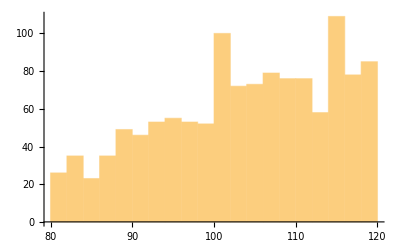

```mathematica
Histogram[nr]
```

Answer: pretty good

```mathematica
Length[alltrain]
```

1233

#### Training

```mathematica
SeedRandom[222444];
test = alltrain[[ti = RandomSample[Range[Length[Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&]]], 223]]];
```

```mathematica
train = Delete[alltrain, List/@ti];
```

```mathematica
p = Predict[train]
```

PredictorFunction[…]

#### Testing

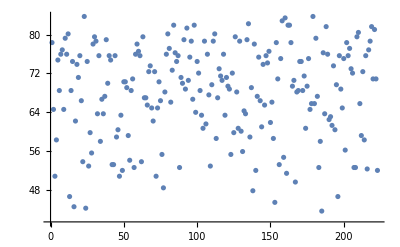

```mathematica
ListPlot[(p/@ test[[All, 1]]), PlotHighlighting->None]
```

Loss:

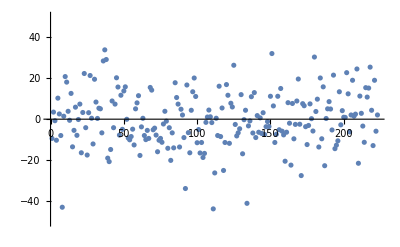

```mathematica
ListPlot[test[[All, 2]] - (p/@ test[[All, 1]]), PlotHighlighting->None, PlotRange->{-50, 50}]
```

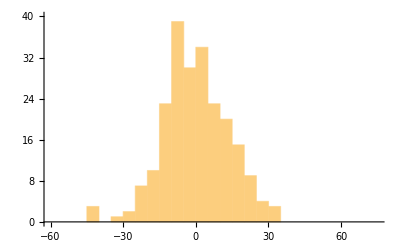

```mathematica
Histogram[test[[All, 2]] - (p/@ test[[All, 1]]), {5}, PlotRange->{{-60, 75},{0, 40} }]
```

Random guess for comparison:

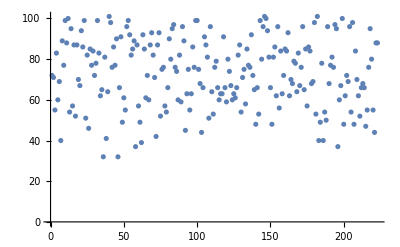

```mathematica
SeedRandom[444555];ListPlot[RandomInteger[{Keys[#][[1, 1]], 101}]&/@ Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&][[ti]], PlotHighlighting->None]
```

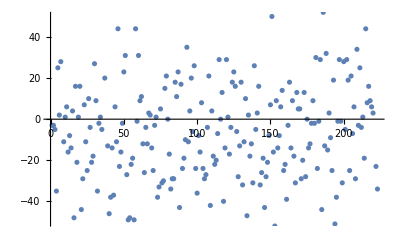

```mathematica
SeedRandom[444555];
With[{aps = Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&]}, ListPlot[test[[All, 2]] -( RandomInteger[{Keys[aps[[#]]][[1, 1]], 101}]&/@ ti), PlotHighlighting->None, PlotRange->{-50, 50}]]
```

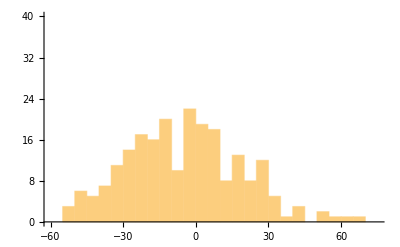

```mathematica
SeedRandom[444555];
Histogram[test[[All, 2]] - (RandomInteger[{Keys[#][[1, 1]], 101}]&/@ Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&][[ti]]), {5}, PlotRange->{{-60, 75},{0, 40} }]
```

#### TCAAASTWA

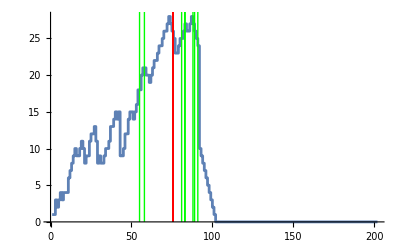
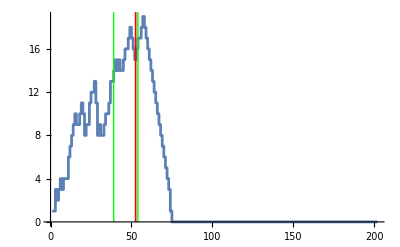
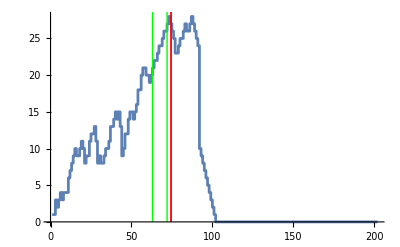
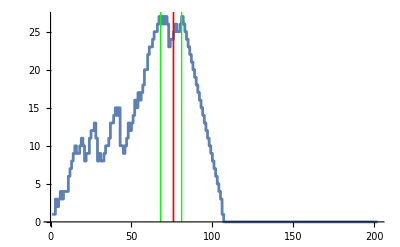
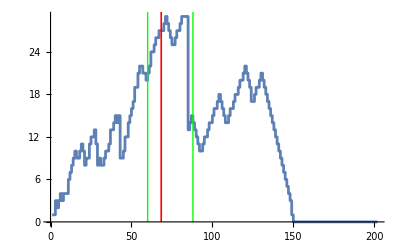
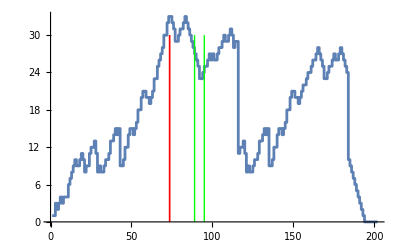
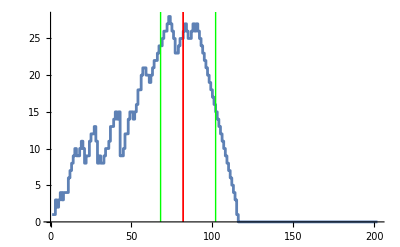
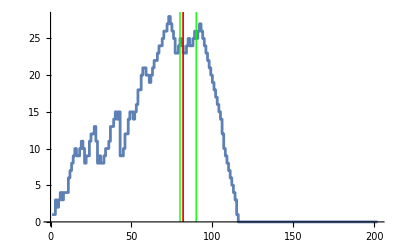
{-Graphics-9,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
With[{aps = Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&], res = p/@alltrain[[All, 1]]},KeyValueMap[Labeled[Show@@{ListStepPlot[#1, PlotHighlighting->None], 
Graphics[
Join[{Green},
Line[{{Keys[First[rh[[#]]]][[1, 1]], 0},{Keys[First[rh[[#]]]][[1, 1]], 30}}]& /@ #2,
{Red},
Line[{{res[[#]], 0},{res[[#]], 30}}]& /@ #2]
]}, Text[Length[#2]]]&,
ReverseSortBy[GroupBy[ti, (If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, aps[[#]], "ReturnPerturbations"->False]& )], Length]][[;;20]]]
```

### Evolution history for main rule

```mathematica
o1 = ;
```

```mathematica
o1["Index"][[23]]
```

2845

```mathematica
rh = Reap[mh = Module[{ru,ca,lt,lts, pcas,fitness},SeedRandom[7896778+ o1["Index"][[23]]];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca=CellularAutomaton[ru,{{1},0},{200,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru, <||>,{lt}}];#,
pcas=Table[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},1],Ceiling[lt/10]];
fitness=Min[lts = Join[{lt},TestCALifeTime/@(First/@pcas)]];
Sow[{ru, Last/@pcas,lts}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]]][[2, 1]];
```

```mathematica
Show[ListStepPlot[mh[[All, 2]]], With[{c =(List/@Cases[Range[1, Length[rh]],x_/;Mod[x, 5] != 0])}, DistributionChart[MapAt[{}&, rh[[All, 3]], c]]], PlotRange->All]
```

-Graphics-

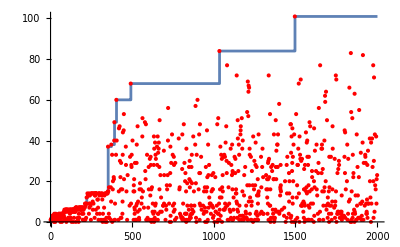

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[Min/@rh[[All, 3]], PlotHighlighting->None, PlotStyle->Red]]
```

### Clustering tree

```mathematica
With[{pcas = PlotCA[#, ImageSize->{20, Automatic}, "Trim"->{1, 1}]&[PerturbedCellularAutomaton[ru, init, {110, {-20, 30}}, #]]&/@ RandomSample[allperts[ru, init, {110, {-20, 30}}], 50]},
ClusteringTree[AssociationThread[pcas->pcas], ImageSize->Large]]
```

-Graphics-

### Medical checkup on big yellow

```mathematica
bigyellowlts500 = TestCALifeTime[PerturbedCellularAutomaton[{297413941736400589979939780692294751544,4,1}, init, {500, {-110, 110}}, #]]&/@ allperts[{297413941736400589979939780692294751544,4,1}, init, {500, {-110, 110}}];
```

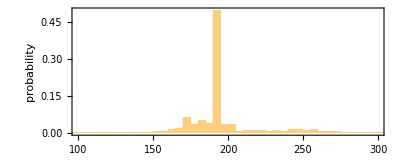

```mathematica
Histogram[bigyellowlts500, 100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}, PlotRange->{{100, 300}, Automatic}]
```

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];PerturbedCellularAutomaton[ru,{{1},0},{200,{-50,150}},1]],"Trim"->{None,None},ImageSize->{Automatic,400}],{i,60}],15]]
```

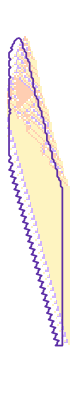
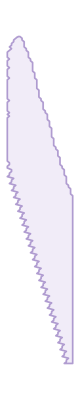
-Graphics--Graphics--Graphics-

```mathematica
Module[{ru={297413941736400589979939780692294751544,4,1},init={{1},0},txspec={200,{-5,214}},aps,pca,ca},ca=CellularAutomaton[ru,init,txspec];
Row[{Show[
PlotCA[CellularAutomaton[ru,init,{200,{-10,30}}],"Trim"->{2,None},ColorRules->(#1->Lighter[#2,.7]&@@@colorrules),Frame->False],
Graphics[{EdgeForm[{Hue[0.73, 0.72, 0.65],AbsoluteDashing[{4,1}],AbsoluteThickness[1.25]}],FaceForm@Transparent,CAPolygon[ca]}],
ImageSize->{Automatic,250}
],Graphics[{GrayLevel[.3],AbsoluteThickness[1.25],Arrowheads[.6],Arrow[{{0,0},{1,0}}]},ImageSize->25],
Graphics[{EdgeForm[{Hue[0.73, 0.43, 0.72, 0.63],AbsoluteDashing[{4,1}],AbsoluteThickness[1.25]}],FaceForm@Hue[0.73, 0.14, 0.93, 0.36],CAPolygon[CellularAutomaton[ru,init,txspec]]},ImageSize->{Automatic,250}]}]]
```

Mean

```mathematica
pcas = With[{ru={297413941736400589979939780692294751544,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-35, 40}}, #, "ReturnPerturbations"->False]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {200, {-35, 40}}]]];
```

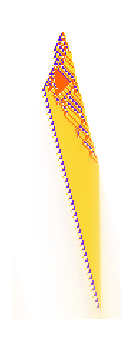

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[pcas,{3,1,2}],{2}]]
```

```mathematica
FeatureSpacePlot[RandomSample[pcas,400],LabelingFunction->PlotCA,LabelingSize->50,Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453]
```

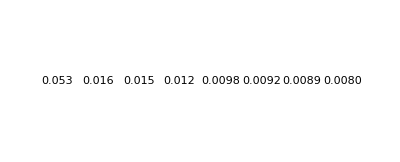

```mathematica
Module[{ru = {297413941736400589979939780692294751544,4,1},init = {{1}, 0},txspec =  {200, {-100, 100}}},GraphicsRow[KeyValueMap[Labeled[Graphics[{EdgeForm[{Hue[0.73, 0.43, 0.72, 0.63],AbsoluteDashing[{4,1}],AbsoluteThickness[1.25]}],FaceForm@Hue[0.73, 0.14, 0.93, 0.36],#1}, Frame->True,FrameTicks->None,ImageSize->{Automatic,200},PlotRange->{{75, 140}, {0, 200}}], Text[NumberForm[N[#2/Length[allperts[ru, init, txspec]],2]]]]&, 
(Take[#, UpTo@8]&@*ReverseSort@*Counts@*(CAPolygon[PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ #&))@allperts[ru, init, txspec]
]]]
```

```mathematica
Module[{ru = {297413941736400589979939780692294751544,4,1},init = {{1}, 0},txspec =  {200, {-100, 100}}},
SeedRandom[6353];abyp = Keys@*(RandomSample[Select[#,#==1&],60]&)@*ReverseSort@*Counts@*(CAPolygon[PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ #&)@allperts[ru, init, txspec]];
```

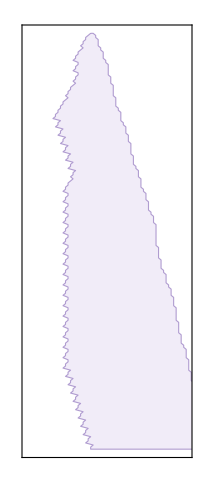
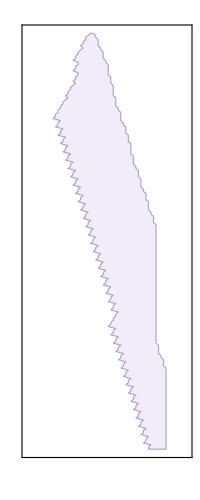
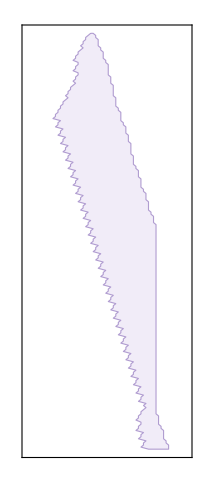
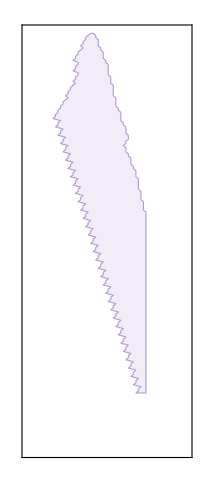
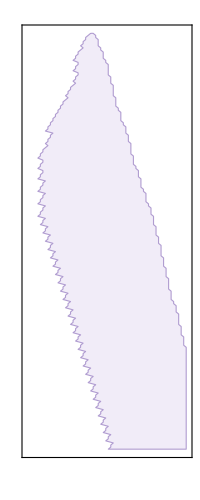
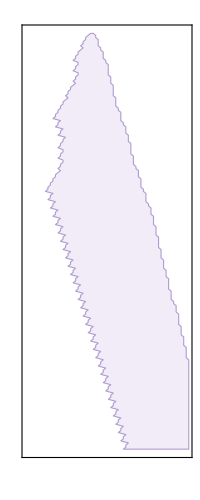
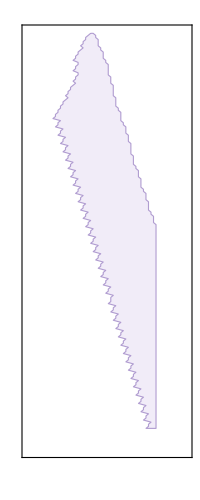
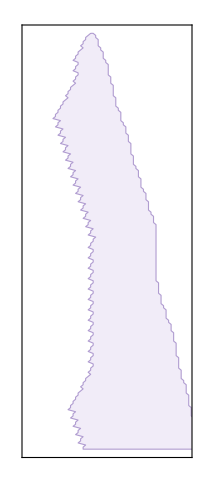

```mathematica
GraphicsGrid@*(Partition[#, 20]&)@*(Graphics[{EdgeForm[{Hue[0.73, 0.43, 0.72, 0.63](*AbsoluteDashing[{4,1}],*)(*AbsoluteThickness[1.25]*)}],FaceForm@Hue[0.73, 0.14, 0.93, 0.36],#1}, Frame->True,FrameTicks->None,ImageSize->{Automatic,200},PlotRange->{{75, 140}, {0, 200}}]&/@#&)@abyp
```

### little yellow?

```mathematica
lilyellowlts = TestCALifeTime[PerturbedCellularAutomaton[{297413941736400589979939780692294751544,4,1}, init, {500, {-110, 110}}, #]]&/@ allperts[{297413946807002990892857386679107573048,4,1}, init, {500, {-110, 110}}];
```

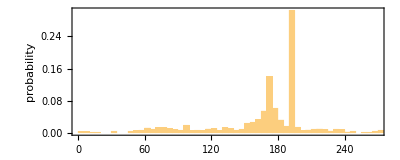

```mathematica
Histogram[lilyellowlts, 100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}(*, PlotRange->{{100, 300}, Automatic}*)]
```

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={297413946807002990892857386679107573048,4,1}},SeedRandom[424324+i];PerturbedCellularAutomaton[ru,{{1},0},{1000,{-50,150}},1]],"Trim"->{1,1},ImageSize->{Automatic,400}],{i,60}],15]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-